```mathematica
ctrl = Import["/Users/yangm/Desktop/ctrl.xlsx"];
ctrl = ctrl[[1]];
case =Import["/Users/yangm/Desktop/case.xlsx"];
case = case[[1]];
g1 = ListPointPlot3D[ctrl, PlotRange-> Full,PlotStyle->Green,PlotStyle->PointSize[Large]];
g2 = ListPointPlot3D[case, PlotRange-> Full,PlotStyle-> Red];
```

```mathematica
Show[g1,g2,PlotLabel->"AD cases(red) and normal controls(green) 3 dimensional",AxesLabel->{"x", "y","z"},LabelStyle->Directive[Blue]]
```

-Graphics3D-

```mathematica
ctrl2d = Import["/Users/yangm/Desktop/ctrl_2d.xlsx"];
ctrl 2d= ctrl2d[[1]];
case2d =Import["/Users/yangm/Desktop/case_2d.xlsx"];
case2d = case2d[[1]];
g12d = ListPlot[ctrl2d, PlotRange-> Full,PlotStyle->Green];
g22d = ListPlot[case2d, PlotRange-> Full,PlotStyle-> Red];
```

Set::write: Tag Times in 2 {«19»,«49»,«49»} {{5.65031,-42.8349,44.8799},{-2.86816,-19.5277,10.8431},{42.3637,-20.5741,6.20027},{-14.9439,-18.2531,3.49329},«43»,{139.81,-40.3759,3.97683},{-98.8566,-0.929901,-18.191},{-31.8833,39.5068,38.162},«138»} is Protected.

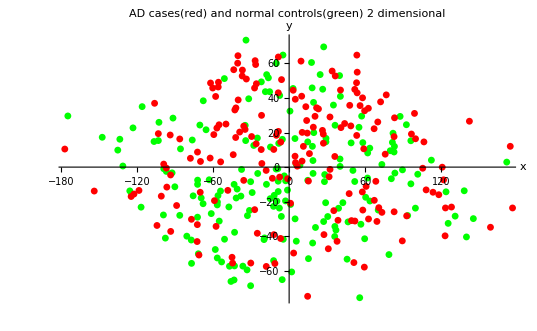

```mathematica
Show[g12d,g22d,PlotLabel->"AD cases(red) and normal controls(green) 2 dimensional",AxesLabel->{"x", "y","z"},LabelStyle->Directive[Blue]]
```